# Anisotropic Viscoelasticity (AI & GST)

## Experimental Data

```mathematica
NotebookDirectory[]
```

D:\Research\

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Research

```mathematica
per3010={{0.01639806551,0.1127719914},{0.0285802913,0.1892042416},{0.03789611103,0.2755402494},{0.04864513379,0.3603102256},{0.06082735958,0.4389522517},{0.07444278841,0.5224557848},{0.08949142027,0.6070685388},{0.1052566537,0.6857538939},{0.121021887,0.7630527228},{0.1367871204,0.8285660801},{0.1525523538,0.8999721732},{0.1683175872,0.9710316348},{0.1840828206,1.028919099},{0.1998480539,1.083686879},{0.2156132873,1.138108027},{0.2313785207,1.187676335},{0.2471437541,1.235858116},{0.2629089875,1.28473316},{0.2786742208,1.329448626},{0.2944394542,1.378670302},{0.3102046876,1.417146401},{0.325969921,1.456662394},{0.3417351544,1.498604808},{0.3575003877,1.541933748},{0.3732656211,1.580063215},{0.3890308545,1.622005629},{0.4047960879,1.664641306},{0.4205613213,1.704503931},{0.4363265546,1.742286767},{0.452091788,1.788042127},{0.4678570214,1.827558121},{0.4836222548,1.871233692},{0.4993874882,1.914735948},{0.5151527216,1.961704519},{0.5309179549,2.009539669},{0.5466831883,2.056334924},{0.5624484217,2.100010495},{0.5782136551,2.15581817},{0.5939788885,2.209546056},{0.6097441218,2.2584211},{0.6255093552,2.316308564},{0.6412745886,2.374196028},{0.657039822,2.433123386},{0.6728050554,2.494130533},{0.6885702887,2.558118712},{0.7043355221,2.619437828},{0.7201007555,2.684084606},{0.7358659889,2.754797436},{0.7516312223,2.818924268},{0.7673964556,2.886864046},{0.783161689,2.955497086},{0.7989269224,3.026556548},{0.8146921558,3.096922747},{0.8297407876,3.169403397},{0.8447894195,3.250827141},{0.8605546529,3.332978812},{0.8763198863,3.398145537},{0.8920851197,3.470591525},{0.907850353,3.543037513},{0.9236155864,3.618603184},{0.9386642183,3.698640402},{0.9537128501,3.775973894},{0.9694780835,3.854659249},{0.9852433169,3.930571552},{0.9995753472,4.012530649},{1.013907378,4.095568156},{1.027522806,4.174210182},{1.040421634,4.257999686},{1.055470266,4.338903483},{1.071235499,4.420015258},{1.087000732,4.509792822},{1.102765966,4.58015902},{1.118531199,4.645325746},{1.134296433,4.704599736},{1.152928072,4.778778881},{1.171559711,4.82418761},{1.174426117,4.823745655},{1.178964594,4.692929808},{1.178009125,4.596970649},{1.178009125,4.513085821},{1.178009125,4.437780124},{1.175859321,4.336737036},{1.172754047,4.226479326},{1.169887641,4.117810345},{1.167976704,4.008823618},{1.164393696,3.899582694},{1.161766157,3.799429294},{1.158660884,3.696298163},{1.154839009,3.578278384},{1.150778267,3.460712527},{1.145762057,3.355856492},{1.141462448,3.248458493},{1.137162839,3.147415405},{1.132863229,3.054633701},{1.12794939,2.9565865},{1.12354741,2.86652833},{1.119145429,2.775743884},{1.113514989,2.681441541},{1.107782176,2.586594491},{1.102151736,2.497398773},{1.096396174,2.408551063},{1.09040459,2.325301726},{1.08433907,2.228313676},{1.078083025,2.141644792},{1.070877198,2.049922241},{1.062636281,1.964130939},{1.057082619,1.882629203},{1.047587649,1.793819319},{1.038988431,1.704215071},{1.030389212,1.615246315},{1.021789994,1.529455013},{1.013190776,1.450018623},{1.004591558,1.371853216},{0.9945591366,1.284949805},{0.9830935124,1.196298794},{0.9716278881,1.112890584},{0.9601622638,1.030435612},{0.947980038,0.9490397906},{0.9343646092,0.8667648736},{0.9193159773,0.7796910358},{0.9057005485,0.7000029253},{0.8920851197,0.6309861137},{0.8763198863,0.557846863},{0.8605546529,0.4947599264},{0.8447894195,0.4283304715},{0.8290241861,0.3595736336},{0.8132589527,0.2968333285},{0.7974937194,0.2441453375},{0.781728486,0.1938837671},{0.7648485391,0.1364584786},{0.7501980192,0.1006398882},{0.7344327858,0.06978968293}};
```

```mathematica
per301={{0.006544794645,0.07365077292},{0.02127493694,0.1335987686},{0.03625772722,0.1755656244},{0.05652775048,0.235826181},{0.0735214436,0.2760849561},{0.08764873066,0.3046820565},{0.1038234506,0.3370425848},{0.1191791974,0.3643274373},{0.1333064845,0.3872051176},{0.1511191508,0.4133015192},{0.1648369512,0.4351393049},{0.180499813,0.4527741835},{0.1998480539,0.4781216134},{0.2127468812,0.490154679},{0.2299453177,0.5147875253},{0.2514433632,0.5367023403},{0.263625589,0.5482567243},{0.2808240254,0.5590600733},{0.3016054694,0.5855773846},{0.3137876952,0.5978250316},{0.3309861316,0.6172075108},{0.3517675756,0.6417316908},{0.3646664029,0.6530219746},{0.3825814409,0.6739250932},{0.4033628849,0.6947663134},{0.4162617122,0.7096714687},{0.4334601486,0.7329728098},{0.4535249911,0.7633993543},{0.4657072169,0.7802109831},{0.4843388563,0.8016588083},{0.5036870973,0.8410448148},{0.5165859246,0.8551081508},{0.533784361,0.8884563038},{0.5538492035,0.9273560633},{0.567567004,0.9515212321},{0.5832298657,0.9799140675},{0.6025781067,1.0223331},{0.6162959071,1.053926087},{0.6319587689,1.087629812},{0.6498738068,1.136143782},{0.6644105804,1.173216848},{0.6785378675,1.203720422},{0.6971695069,1.252149797},{0.7117062806,1.290328783},{0.7266525408,1.333360611},{0.7444652071,1.380750091},{0.7596929893,1.426505452},{0.7736070021,1.467176884},{0.7917609072,1.515936384},{0.8079356272,1.569218601},{0.8227539229,1.609050276},{0.8390566074,1.670187411},{0.855896743,1.727728243},{0.8711245253,1.778249787},{0.885635706,1.830677804},{0.904983947,1.884482719},{0.9250487894,1.923921683},{0.9379476168,1.943976792},{0.9544294517,1.985578765},{0.9737776926,2.035883664},{0.9883144663,2.073072274},{1.003695806,2.112835861},{1.021073393,2.17626943},{1.036997871,2.239086764},{1.053013346,2.298036131},{1.068369093,2.341959296},{1.086181759,2.389002145},{1.09989956,2.429310439},{1.115664793,2.468133169},{1.13304238,2.529876909},{1.149242693,2.581828308},{1.168932173,2.651732331},{1.167771961,2.61952201},{1.163881838,2.50121172},{1.157466548,2.352797308},{1.150220911,2.216209084},{1.143612252,2.113598451},{1.137162839,2.041915052},{1.129996823,1.954326219},{1.121397605,1.84745477},{1.11423159,1.775771371},{1.104199169,1.690446097},{1.093450146,1.585378232},{1.081984522,1.491325546},{1.070621269,1.407985425},{1.060629797,1.338045088},{1.046871047,1.240710957},{1.028812689,1.140153153},{1.012474175,1.051796779},{0.9959127173,0.9706464886},{0.9787939032,0.8931695296},{0.9659746983,0.8431246039},{0.9502094649,0.7855067424},{0.9336480077,0.7294294654},{0.9170865504,0.6685763763},{0.9014009394,0.6177794528},{0.8863523075,0.5866172792},{0.8705870741,0.5346225512},{0.8548218408,0.4906003481},{0.8395940585,0.4680259704},{0.823291374,0.4208407548},{0.8075261406,0.3876507867},{0.7881778996,0.345535057},{0.7740847365,0.3283767968},{0.7587972374,0.2940602763},{0.7394489965,0.2546598269},{0.7248780989,0.2260627265},{0.7115015373,0.2074023963},{0.6941239505,0.1801484931},{0.6775823988,0.1523457566},{0.6642058372,0.1307968304},{0.6434243931,0.1005532303},{0.6281966109,0.08577806179},{0.6140437309,0.07256273509}};
```

```mathematica
per3001={{0.003984753985,0.008056784661},{0.01427581428,0.02713864307},{0.02425502426,0.04373156342},{0.03672903673,0.06032448378},{0.05045045045,0.07333333333},{0.06417186417,0.08997050147},{0.07914067914,0.1041297935},{0.09286209286,0.1200589971},{0.1065835066,0.1339970501},{0.1215523216,0.1373156342},{0.1365211365,0.1446165192},{0.1514899515,0.1528023599},{0.1664587665,0.1627581121},{0.1814275814,0.1676253687},{0.1963963964,0.1744837758},{0.2113652114,0.1797935103},{0.2263340263,0.1893067847},{0.2413028413,0.1886430678},{0.2562716563,0.1979351032},{0.2712404712,0.1997050147},{0.2862092862,0.2103244838},{0.3011781012,0.2109882006},{0.3161469161,0.2143067847},{0.3311157311,0.2193952802},{0.3460845461,0.227359882},{0.3610533611,0.2324483776},{0.376022176,0.2362094395},{0.390990991,0.2419616519},{0.405959806,0.2490412979},{0.4209286209,0.2512536873},{0.4358974359,0.2552359882},{0.4508662509,0.2545722714},{0.4658350658,0.2658554572},{0.4808038808,0.2731563422},{0.4957726958,0.2813421829},{0.5107415107,0.2873156342},{0.5257103257,0.2886430678},{0.5406791407,0.2963864307},{0.5556479556,0.3041297935},{0.5706167706,0.3127581121},{0.5855855856,0.3193952802},{0.6005544006,0.3313421829},{0.6155232155,0.3333333333},{0.6304920305,0.3419616519},{0.6454608455,0.3516961652},{0.6604296604,0.3589970501},{0.6753984754,0.3643067847},{0.6881219681,0.3656342183},{0.7003465003,0.3806784661},{0.7153153153,0.3868731563},{0.7302841303,0.3961651917},{0.7452529453,0.4087758112},{0.7602217602,0.4158554572},{0.7751905752,0.4220501475},{0.7901593902,0.4357669617},{0.8051282051,0.4432890855},{0.8200970201,0.456120944},{0.8350658351,0.4654129794},{0.85003465,0.4802359882},{0.865003465,0.4884218289},{0.8774774775,0.4990412979},{0.88995149,0.516519174},{0.9049203049,0.5247050147},{0.9198891199,0.541740413},{0.9323631324,0.5567846608},{0.9435897436,0.5724483776},{0.9573111573,0.5862094395},{0.9697851698,0.5985988201},{0.9822591823,0.612979351},{0.9972279972,0.627359882},{1.012196812,0.6390855457},{1.023423423,0.6554572271},{1.030907831,0.6700589971},{1.042134442,0.6851032448},{1.055855856,0.7041297935},{1.068329868,0.71820059},{1.082051282,0.7353244838},{1.090783091,0.7519174041},{1.102009702,0.7709439528},{1.115731116,0.7848377581},{1.126957727,0.7983775811},{1.139431739,0.8160766962},{1.151905752,0.8305678466},{1.158142758,0.8461651917},{1.168121968,0.8628908555},{1.18040733,0.8809324812},{1.188095146,0.897335573},{1.189773106,0.8966076696},{1.189253998,0.880899705},{1.187635071,0.8634218289},{1.186209286,0.8445058997},{1.183090783,0.8232669617},{1.178600139,0.7967846608},{1.175606376,0.7718289086},{1.174358974,0.7528023599},{1.168620929,0.7282890855},{1.165627166,0.7061651917},{1.161635482,0.6847492625},{1.156146916,0.6574041298},{1.150658351,0.6360988201},{1.145668746,0.6151917404},{1.140679141,0.5997050147},{1.136687457,0.5825368732},{1.130699931,0.5643067847},{1.126957727,0.5491519174},{1.121718642,0.5310324484},{1.115731116,0.5126474926},{1.109494109,0.4919616519},{1.103257103,0.4734882006},{1.097020097,0.4552359882},{1.08978517,0.4375811209},{1.082942283,0.4183522967},{1.074816355,0.3990855457},{1.065419265,0.3780235988},{1.057352737,0.3613864307},{1.049084249,0.3453434471},{1.038808039,0.3253687316},{1.02966043,0.3081120944},{1.017186417,0.2922935103},{1.008870409,0.2742625369},{0.9977625978,0.2558364939},{0.9865003465,0.2408554572},{0.9753984754,0.2262536873},{0.9628353628,0.211462284},{0.9492921493,0.19325748},{0.9376645877,0.1791297935},{0.924047124,0.1627581121},{0.9122661123,0.1510324484},{0.8974358974,0.1368731563},{0.8826452826,0.1236620312},{0.8717394317,0.1120943953},{0.86001386,0.1014749263},{0.845045045,0.09306784661},{0.8300762301,0.07448377581},{0.8149292149,0.06525495154},{0.8006732007,0.05217024863},{0.7851697852,0.04328908555},{0.7702009702,0.03266961652},{0.7552321552,0.01895280236},{0.7402633403,0.01032448378}};
```

```mathematica
per30001={{0.004283031044,0.008786238179},{0.02038438426,0.02419339511},{0.03765868375,0.03816400316},{0.05589266653,0.04888705759},{0.07700569923,0.05707557187},{0.09811873193,0.06582112795},{0.1192317646,0.07428816313},{0.1403447973,0.07841027237},{0.16145783,0.08325653592},{0.1825708627,0.0922806129},{0.2036838954,0.08871554545},{0.2247969281,0.09846377675},{0.2459099608,0.0996335645},{0.2670229935,0.1065873028},{0.2881360262,0.1064294743},{0.3092490589,0.1054267991},{0.3295623555,0.1146551247},{0.3514751243,0.1154535513},{0.3697091071,0.1188932843},{0.3875001591,0.1222751707},{0.4090561226,0.1259259369},{0.4301691553,0.1273742456},{0.451282188,0.129992342},{0.4723952207,0.1335017052},{0.4935082534,0.144029795},{0.5146212861,0.1459237371},{0.5359088067,0.1478176792},{0.5478903073,0.1531900378},{0.5683635511,0.1567940097},{0.5894765838,0.1644175245},{0.6105896165,0.1678711836},{0.627863916,0.1703858294},{0.6451382155,0.1822985659},{0.6662512482,0.187311942},{0.6854449143,0.1942440176},{0.7046385804,0.2035775622},{0.7257516131,0.2102063595},{0.7468646458,0.2211243785},{0.7622195787,0.2339363397},{0.7737357783,0.2471939342},{0.794848811,0.2549368151},{0.8159618437,0.2656877216},{0.8370748764,0.2780540493},{0.8543491759,0.2915344606},{0.8716234754,0.3029538172},{0.8879380915,0.3142060614},{0.9042527077,0.3304716816},{0.9240221838,0.3368163876},{0.9407206733,0.352419128},{0.9555272157,0.3645387658},{0.9691621967,0.3781544587},{0.9887048385,0.3935845162},{1.002865721,0.4089228295},{1.022604763,0.4196664506},{1.032850271,0.4343042709},{1.047910856,0.4451539879},{1.061280384,0.4616341981},{1.082114013,0.4724306867},{1.091019963,0.4917762561},{1.106745885,0.5052296166},{1.122176651,0.5172686178},{1.130772401,0.5285827555},{1.137455751,0.542482302},{1.137455751,0.5346360056},{1.13341466,0.5135603035},{1.128392168,0.4964752529},{1.125477512,0.4779113589},{1.116221992,0.4567307733},{1.10930504,0.4345085196},{1.102907152,0.4210281083},{1.093502255,0.4061179564},{1.087689316,0.3903616316},{1.076995703,0.37670615},{1.069318236,0.3632257387},{1.057802036,0.348060276},{1.043406787,0.3332777796},{1.033809954,0.3213547643},{1.023253437,0.3073783206},{1.011737238,0.2945981904},{1.000395526,0.2786667953},{0.9885446136,0.266945054},{0.9724712494,0.2527137947},{0.9541562396,0.2367772528},{0.9388013067,0.2219599412},{0.9196076406,0.2107076971},{0.8992328258,0.197690059},{0.8850590416,0.1834285649},{0.8671941678,0.169378053},{0.8474714455,0.1594877047},{0.8304443372,0.1444197243},{0.8119754669,0.1328803894},{0.7919697611,0.1205170611},{0.7716687681,0.1060138354},{0.750703379,0.09395173826},{0.7338556054,0.07530321706},{0.7173064,0.06632989278},{0.6973724068,0.06214863102},{0.683909421,0.04778411484},{0.6655314857,0.04053839378}};
```

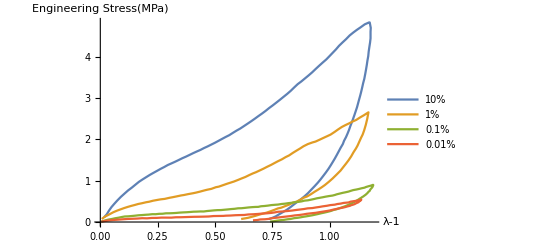

```mathematica
ListLinePlot[{per3010,per301,per3001,per30001},PlotLegends->{"10%","1%","0.1%","0.01%"},AxesLabel->{"λ-1","Engineering Stress(MPa)"}]
```

```mathematica
Export["data.xls",{per3010,per301,per3001,per30001}]
```

data.xls

## λ[t] and λ'[t] Computation

### (*Strain Rates*)

```mathematica
{ld1,ld2,ld3,ld4}={0.1,0.01,0.001,0.0001}
```

{0.1,0.01,0.001,0.0001}

```mathematica
time1a=per3010[[;;,1]]/ld1 ;
```

```mathematica
time2a=per301[[;;,1]]/ld2;
```

```mathematica
time3a=per3001[[;;,1]]/ld3;
```

```mathematica
time4a=per30001[[;;,1]]/ld4 ;
```

```mathematica
time1b=time1a[[Position[time1a,Max[time1a]][[1,1]]+1;;]]+2 (Max[time1a]-time1a[[Position[time1a,Max[time1a]][[1,1]]+1;;]]);
```

```mathematica
time1=Join[time1a[[1;;Position[time1a,Max[time1a]][[1,1]]]],time1b];
```

```mathematica
time2b=time2a[[Position[time2a,Max[time2a]][[1,1]]+1;;]]+2 (Max[time2a]-time2a[[Position[time2a,Max[time2a]][[1,1]]+1;;]]);
```

```mathematica
time2=Join[time2a[[1;;Position[time2a,Max[time2a]][[1,1]]]],time2b];
```

```mathematica
time3b=time3a[[Position[time3a,Max[time3a]][[1,1]]+1;;]]+2 (Max[time3a]-time3a[[Position[time3a,Max[time3a]][[1,1]]+1;;]]);
```

```mathematica
time3=Join[time3a[[1;;Position[time3a,Max[time3a]][[1,1]]]],time3b];
```

```mathematica
time4b=time4a[[Position[time4a,Max[time4a]][[1,1]]+1;;]]+2 (Max[time4a]-time4a[[Position[time4a,Max[time4a]][[1,1]]+1;;]]);
```

```mathematica
time4=Join[time4a[[1;;Position[time4a,Max[time4a]][[1,1]]]],time4b];
```

### (*λ[t] and λ'[t]*)

```mathematica
Logist
```

Logist

```mathematica
ldot[p_,q_,m_,x_]:=-2 p(LogisticSigmoid[ m (x-q)]-0.5);(*p=peak,q=point where unloading occurs, m=sharpness of transition *)
```

```mathematica
lda=DSolveValue[{l'[t]-ldot[a,b,c,t]==0,l[0]==1},l,{t,0,10}];
```

```mathematica
lda1=Simplify[lda[t]/.{a->ld1,b->Max[time1a],c->15}];
```

```mathematica
dlda1=Simplify[lda'[t]/.{a->ld1,b->Max[time1a],c->15}];
```

```mathematica
lda2=Simplify[lda[t]/.{a->ld2,b->Max[time2a],c->0.5}];
```

```mathematica
dlda2=Simplify[lda'[t]/.{a->ld2,b->Max[time2a],c->0.5}];
```

```mathematica
lda3=Simplify[lda[t]/.{a->ld3,b->Max[time3a],c->0.06}];
```

```mathematica
dlda3=Simplify[lda'[t]/.{a->ld3,b->Max[time3a],c->0.06}];
```

```mathematica
lda4=Simplify[lda[t]/.{a->ld4,b->Max[time4a],c->0.01}];
```

```mathematica
dlda4=Simplify[lda'[t]/.{a->ld4,b->Max[time4a],c->0.01}];
```

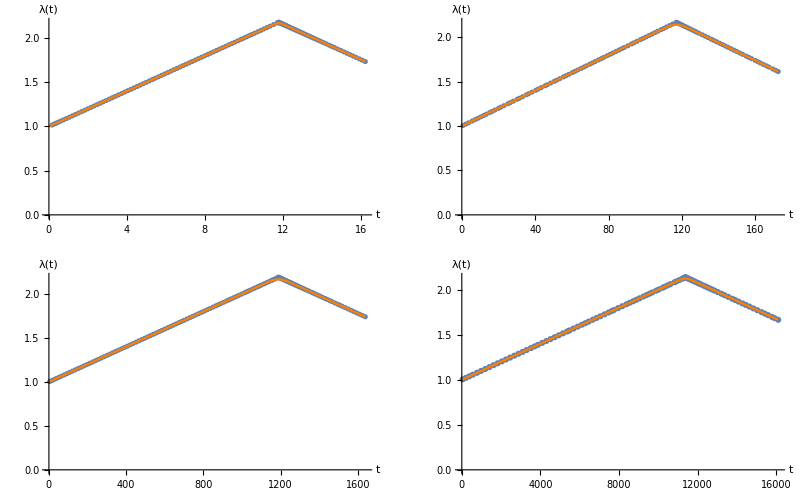

```mathematica
GraphicsGrid[{{Show[ListPlot[Table[{time1[[i]],per3010[[i,1]]+1},{i,1,132}],AxesLabel->{"t","λ(t)"}],Plot[lda1,{t,0,Max[time1]},PlotRange->{{0,20},{0,2.4}},PlotStyle->{Orange},AxesLabel->{"t","λ"}]],Show[ListPlot[Table[{time2[[i]],per301[[i,1]]+1},{i,1,114}],AxesLabel->{"t","λ(t)"}],Plot[lda2,{t,0,Max[time2]},PlotRange->{{0,20},{0,2.4}},PlotStyle->{Orange}]]},{Show[ListPlot[Table[{time3[[i]],per3001[[i,1]]+1},{i,1,140}],AxesLabel->{"t","λ(t)"}],Plot[lda3,{t,0,Max[time3]},PlotRange->{{0,20},{0,2.4}},PlotStyle->{Orange}]],Show[ListPlot[Table[{time4[[i]],per30001[[i,1]]+1},{i,1,99}],AxesLabel->{"t","λ(t)"}],Plot[lda4,{t,0,Max[time4]},PlotRange->{{0,20},{0,2.4}},PlotStyle->{Orange}]]}}]
```

```mathematica
Max[time2]
```

172.382

```mathematica
NumberForm[Max[time4],16]
```

16093.800163

```mathematica
lda1
```

3.35793-0.1 t-0.0133333 Log[1.+6.34852×10^76 ⅇ^(-15. t)]

```mathematica
dlda1
```

(6.34852×10^75-0.1 ⅇ^(15. t))/(6.34852×10^76+1. ⅇ^(15. t))

```mathematica
PrintMatlab[lda4]
```

0.327491E1+(-0.1E-3).*t+(-0.2E-1).*log(0.1E1+0.250655E50.* ...
  exp(1).^((-0.1E-1).*t));

```mathematica
PrintMatlab[dlda4]
```

(0.250655E46+(-0.1E-3).*exp(1).^(0.1E-1.*t)).*(0.250655E50+ ...
  0.1E1.*exp(1).^(0.1E-1.*t)).^(-1);

## Kinematics

```mathematica
F={{1/(√l[t]),0,0},{0,1/(√l[t]),0},{0,0,l[t]}}
```

{{1/(√l[t]),0,0},{0,1/(√l[t]),0},{0,0,l[t]}}

```mathematica
F//MatrixForm
```

(1/(√l[t]) | 0 | 0
0 | 1/(√l[t]) | 0
0 | 0 | l[t])

```mathematica
Det[F]
```

1

```mathematica
L=D[F,t].Inverse[F]
```

{{-l'[t]/(2 l[t]),0,0},{0,-l'[t]/(2 l[t]),0},{0,0,l'[t]/l[t]}}

```mathematica
n={0,0,1}
```

{0,0,1}

```mathematica
n1={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]}
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[ϕ]}

```mathematica
G={{1/(√g33[t]),0,0},{0,1/(√g33[t]),0},{0,0,g33[t]}}
```

{{1/(√g33[t]),0,0},{0,1/(√g33[t]),0},{0,0,g33[t]}}

```mathematica
G//MatrixForm
```

(1/(√g33[t]) | 0 | 0
0 | 1/(√g33[t]) | 0
0 | 0 | g33[t])

```mathematica
Lp=D[G,t].Inverse[G]
```

{{-g33'[t]/(2 g33[t]),0,0},{0,-g33'[t]/(2 g33[t]),0},{0,0,g33'[t]/g33[t]}}

```mathematica
Fe=F.Inverse[G]//Simplify
```

{{(√g33[t])/(√l[t]),0,0},{0,(√g33[t])/(√l[t]),0},{0,0,l[t]/g33[t]}}

```mathematica
Ce=Transpose[Fe].Fe
```

{{g33[t]/l[t],0,0},{0,g33[t]/l[t],0},{0,0,l[t]^2/g33[t]^2}}

```mathematica
Be=Fe.Transpose[Fe]
```

{{g33[t]/l[t],0,0},{0,g33[t]/l[t],0},{0,0,l[t]^2/g33[t]^2}}

### Functions

```mathematica
sym[A_]:=1/2(A+Transpose[A])//Simplify
```

```mathematica
skw[A_]:=1/2 (A-Transpose[A]) //Simplify
```

```mathematica
dev[A_]:=A-Tr[A]/3 IdentityMatrix[3]//Simplify
```

```mathematica
Dp=sym[Lp]
```

{{-g33'[t]/(2 g33[t]),0,0},{0,-g33'[t]/(2 g33[t]),0},{0,0,g33'[t]/g33[t]}}

## Strain Energy Potential

```mathematica
W1=mu0/2 (I1-3)
```

1/2 (-3+I1) mu0

```mathematica
W2=mu1/(2mu2) (Exp[mu2 (I4-1)^2]-1)
```

((-1+ⅇ^((-1+I4)^2 mu2)) mu1)/(2 mu2)

```mathematica
W=W1+W2
```

1/2 (-3+I1) mu0+((-1+ⅇ^((-1+I4)^2 mu2)) mu1)/(2 mu2)

```mathematica
D[W1,I1] 2 Tr[Ce.Dp]
```

mu0 (-g33'[t]/l[t]+(l[t]^2 g33'[t])/g33[t]^3)

## Order Parameter

```mathematica
binitial=2.012747764451281
```

2.01275

## Probability Distribution

Vonmises distribution

```mathematica
Exp[b Cos[2 θ]]
```

ⅇ^(b Cos[2 θ])

```mathematica
factor=Integrate[Exp[b Cos[2 θ]] Sin[θ],{θ,0,π},{ϕ,0,2 π}]
```

(√2 ⅇ^-b π^(3/2) Erfi[√2 √b])/(√b)

```mathematica
(4 π)/factor Exp[b Cos[2 θ]]//Simplify
```

(2 √b ⅇ^(2 b Cos[θ]^2) √(2/π))/Erfi[√2 √b]

```mathematica
rho=(2 √b ⅇ^(2 b Cos[θ]^2) √(2/π))/Erfi[√2 √b]
```

(2 √b ⅇ^(2 b Cos[θ]^2) √(2/π))/Erfi[√2 √b]

## Evaluation of Rho Hat

```mathematica
M={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]} (*Arbritrary fiber in the reference configuration*)
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
ToSphericalCoordinates[M]
```

{√(Cos[θ]^2+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2),ArcTan[Cos[θ],√(Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2)],ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]}

```mathematica
Assuming[{0<=θ<=π,0<=ϕ<=2 π},Simplify[ToSphericalCoordinates[M]]]
```

{1,θ,ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]}

```mathematica
G1={{1/(√g33),0,0},{0,1/(√g33),0},{0,0,g33}}
```

{{1/(√g33),0,0},{0,1/(√g33),0},{0,0,g33}}

```mathematica
G1//MatrixForm
```

(1/(√g33) | 0 | 0
0 | 1/(√g33) | 0
0 | 0 | g33)

```mathematica
MtoMhat=Assuming[{g33>0,0<=θ<=π,0<=ϕ<=2 π},Simplify[(G1.M)/(√((G1.M).Transpose[(G1.M)]))]]
```

{(√2 Cos[ϕ] Sin[θ])/(√(1+g33^3+(-1+g33^3) Cos[2 θ])),(√2 Sin[θ] Sin[ϕ])/(√(1+g33^3+(-1+g33^3) Cos[2 θ])),√2 g33 Cos[θ] √(g33/(1+g33^3+(-1+g33^3) Cos[2 θ]))}

```mathematica
Assuming[{g33>0,0<=θ<=π,0<=ϕ<=2 π},Simplify[ToSphericalCoordinates[MtoMhat]]]
```

{1,ArcTan[g33 Cos[θ] √(g33/(1+g33^3+(-1+g33^3) Cos[2 θ])),Sin[θ]/(√(1+g33^3+(-1+g33^3) Cos[2 θ]))],ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]}

### Hat as a function of no Hat

```mathematica
hnohat={1,ArcTan[g33 Cos[θ] √(g33/(1+g33^3+(-1+g33^3) Cos[2 θ])),Sin[θ]/(√(1+g33^3+(-1+g33^3) Cos[2 θ]))],ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]}
```

{1,ArcTan[g33 Cos[θ] √(g33/(1+g33^3+(-1+g33^3) Cos[2 θ])),Sin[θ]/(√(1+g33^3+(-1+g33^3) Cos[2 θ]))],ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]}

```mathematica
M1={Sin[θ̂] Cos[ϕ̂],Sin[θ̂] Sin[ϕ̂],Cos[θ̂]}
```

{Cos[ϕ̂] Sin[θ̂],Sin[θ̂] Sin[ϕ̂],Cos[θ̂]}

```mathematica
MhattoM=Assuming[{g33>0,0<=θ̂<=π,0<=ϕ̂<=2 π},Simplify[(Inverse[G1].M1)/(√((Inverse[G1].M1).Transpose[(Inverse[G1].M1)]))]]
```

{(√2 g33^(3/2) Cos[ϕ̂] Sin[θ̂])/(√(1+g33^3-(-1+g33^3) Cos[2 θ̂])),(√2 g33^(3/2) Sin[θ̂] Sin[ϕ̂])/(√(1+g33^3-(-1+g33^3) Cos[2 θ̂])),(√2 Cos[θ̂])/(√(1+g33^3-(-1+g33^3) Cos[2 θ̂]))}

```mathematica
nohath=Assuming[{g33>0,0<=θ̂<=π,0<=ϕ̂<=2 π},Simplify[ToSphericalCoordinates[MhattoM]]]
```

{1,ArcTan[Cos[θ̂],g33^(3/2) Sin[θ̂]],ArcTan[Cos[ϕ̂] Sin[θ̂],Sin[θ̂] Sin[ϕ̂]]}

```mathematica
rho
```

(2 √b ⅇ^(2 b Cos[θ]^2) √(2/π))/Erfi[√2 √b]

```mathematica
nohath[[2]]
```

ArcTan[Cos[θ̂],g33^(3/2) Sin[θ̂]]

```mathematica
Assuming[{g33>0,0<=θ̂<=π,0<=ϕ̂<=2 π},Simplify[((2 √b ⅇ^(2 b Cos[θ]^2) √(2/π))/Erfi[√2 √b] Sin[θ] /.{θ->nohath[[2]]}) D[nohath[[2]],θ̂]]]
```

(2 √b ⅇ^((2 b Cos[θ̂]^2)/(Cos[θ̂]^2+g33^3 Sin[θ̂]^2)) g33^3 √(2/π) Sin[θ̂])/(Erfi[√2 √b] (Cos[θ̂]^2+g33^3 Sin[θ̂]^2)^(3/2))

```mathematica
((2 √b ⅇ^((2 b Cos[θ̂]^2)/(Cos[θ̂]^2+g33^3 Sin[θ̂]^2)) g33^3 √(2/π) Sin[θ̂])/(Erfi[√2 √b] (Cos[θ̂]^2+g33^3 Sin[θ̂]^2)^(3/2)))/Sin[θ̂]//Simplify
```

(2 √b ⅇ^((2 b Cos[θ̂]^2)/(Cos[θ̂]^2+g33^3 Sin[θ̂]^2)) g33^3 √(2/π))/(Erfi[√2 √b] (Cos[θ̂]^2+g33^3 Sin[θ̂]^2)^(3/2))

#### Rho Hat

```mathematica
rhohat=(2 √b ⅇ^((2 b Cos[θ̂]^2)/(Cos[θ̂]^2+g33^3 Sin[θ̂]^2)) g33^3 √(2/π))/(Erfi[√2 √b] (Cos[θ̂]^2+g33^3 Sin[θ̂]^2)^(3/2))
```

(2 √b ⅇ^((2 b Cos[θ̂]^2)/(Cos[θ̂]^2+g33^3 Sin[θ̂]^2)) g33^3 √(2/π))/(Erfi[√2 √b] (Cos[θ̂]^2+g33^3 Sin[θ̂]^2)^(3/2))

## Evaluation of Kappa Hat

kappa=1/4 ∫_0^π ρ(θ) Sin[θ]^3 ⅆθ

```mathematica
kappa=Integrate[1/4 rho Sin[θ]^3,{θ,0,π}]//Simplify
```

1/8 (4+1/b-(2 ⅇ^(2 b) √(2/π))/(√b Erfi[√2 √b]))

```mathematica
kpa[b_]:=1/8 (4+1/b-(2 ⅇ^(2 b) √(2/π))/(√b Erfi[√2 √b]))
```

```mathematica
Assuming[{g33>0,0<=θ̂<=π},FullSimplify[(1/4 rho Sin[θ]^3/.{θ->nohath[[2]]}) D[nohath[[2]],θ̂]]]/.{θ̂->θ} (*Integrand of Khat *)
```

(√b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) g33^6 Sin[θ]^3)/(√(2 π) Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(5/2))

```mathematica
1/4 rhohat Sin[θ̂]^3/.{θ̂->θ}//Simplify (*Integrand of Kappa Hat*)
```

(√b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) g33^3 Sin[θ]^3)/(√(2 π) Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))

```mathematica
khat1[g33_?NumericQ,b_?NumericQ]:=NIntegrate[(√b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) g33^3 Sin[θ]^3)/(√(2 π) Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),{θ,0,π}]
```

```mathematica
khat1data=Table[{g33,khat1[g33,binitial]},{g33,1,10,0.1}];
```

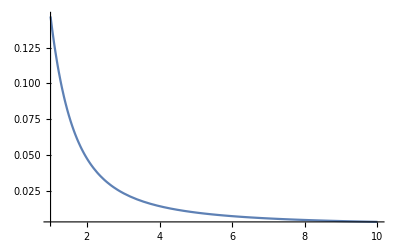

```mathematica
Plot[khat[g33],{g33,1,10},PlotRange->All]
```

```mathematica
khat[g33_]:=Interpolation[khat1data][g33]
```

```mathematica
Manipulate[Plot[khatn[g33,b],{b,0.01,20},PlotRange->All],{g33,1,10}]
```

```mathematica
Manipulate[Plot[{khat[g33,b],kpa[b]},{b,0.01,50},PlotRange->{{0,50},{0,1/3}}],{g33,1,20}]
```

## RhoHat Dot and Khat Dot

```mathematica
rhohat/.{g33->g33[t]}
```

(2 √b ⅇ^((2 b Cos[θ̂]^2)/(Cos[θ̂]^2+g33[t]^3 Sin[θ̂]^2)) √(2/π) g33[t]^3)/(Erfi[√2 √b] (Cos[θ̂]^2+g33[t]^3 Sin[θ̂]^2)^(3/2))

```mathematica
Assuming[{g33>0,0<=θ̂<=π,0<=ϕ̂<=2 π},Simplify[D[rhohat/.{g33->g33[t]},t]]]
```

(3 √b ⅇ^((2 b Cos[θ̂]^2)/(Cos[θ̂]^2+g33[t]^3 Sin[θ̂]^2)) g33[t]^2 (8 Cos[θ̂]^4-4 g33[t]^6 Sin[θ̂]^4-(-1+4 b) g33[t]^3 Sin[2 θ̂]^2) g33'[t])/(2 √(2 π) Erfi[√2 √b] (Cos[θ̂]^2+g33[t]^3 Sin[θ̂]^2)^(7/2))

```mathematica
Assuming[{g33>0,0<=θ̂<=π,0<=ϕ̂<=2 π},Simplify[D[(2 √b ⅇ^((2 b Cos[θ̂]^2)/(Cos[θ̂]^2+g33[t]^3 Sin[θ̂]^2)) √(2/π) g33[t]^3)/(Erfi[√2 √b] (Cos[θ̂]^2+g33[t]^3 Sin[θ̂]^2)^(3/2)),t]]]
```

(3 √b ⅇ^((2 b Cos[θ̂]^2)/(Cos[θ̂]^2+g33[t]^3 Sin[θ̂]^2)) g33[t]^2 (8 Cos[θ̂]^4-4 g33[t]^6 Sin[θ̂]^4-(-1+4 b) g33[t]^3 Sin[2 θ̂]^2) g33'[t])/(2 √(2 π) Erfi[√2 √b] (Cos[θ̂]^2+g33[t]^3 Sin[θ̂]^2)^(7/2))

Rho Hat Dot

```mathematica
rhohatdot=(3 √b ⅇ^((2 b Cos[θ̂]^2)/(Cos[θ̂]^2+g33[t]^3 Sin[θ̂]^2)) g33[t]^2 (8 Cos[θ̂]^4-4 g33[t]^6 Sin[θ̂]^4-(-1+4 b) g33[t]^3 Sin[2 θ̂]^2) g33'[t])/(2 √(2 π) Erfi[√2 √b] (Cos[θ̂]^2+g33[t]^3 Sin[θ̂]^2)^(7/2))
```

(3 √b ⅇ^((2 b Cos[θ̂]^2)/(Cos[θ̂]^2+g33[t]^3 Sin[θ̂]^2)) g33[t]^2 (8 Cos[θ̂]^4-4 g33[t]^6 Sin[θ̂]^4-(-1+4 b) g33[t]^3 Sin[2 θ̂]^2) g33'[t])/(2 √(2 π) Erfi[√2 √b] (Cos[θ̂]^2+g33[t]^3 Sin[θ̂]^2)^(7/2))

Integrand of Kappa hat dot

```mathematica
ikhatdot=(√b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) g33^3 Sin[θ]^3)/(√(2 π) Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))
```

(√b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) g33^3 Sin[θ]^3)/(√(2 π) Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))

```mathematica
Assuming[{g33>0,0<=θ<=π},Simplify[D[ikhatdot,g33]]]
```

(3 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) g33^2 Sin[θ]^3 (2 Cos[θ]^4+g33^3 Cos[θ]^2 Sin[θ]^2-g33^3 (g33^3 Sin[θ]^4+b Sin[2 θ]^2)))/(2 √(2 π) Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(7/2))

```mathematica
kbar1[g33_?NumericQ,b_?NumericQ]:=NIntegrate[(3 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) g33^2 Sin[θ]^3 (2 Cos[θ]^4+g33^3 Cos[θ]^2 Sin[θ]^2-g33^3 (g33^3 Sin[θ]^4+b Sin[2 θ]^2)))/(2 √(2 π) Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(7/2)),{θ,0,π}]
```

```mathematica
kbardata=Table[{g33,kbar1[g33,binitial]},{g33,1,10,0.1}];
```

```mathematica
kbar[g33_]:=Interpolation[kbardata][g33]
```

```mathematica
khatdot=kbar[g33[t]] g33'[t]
```

InterpolatingFunction[…][g33[t]] g33'[t]

## Dissipation

```mathematica
hphat=khat[g33[t]] IdentityMatrix[3]+(1-3 khat[g33[t]]) TensorProduct[n,n]//Simplify
```

{{InterpolatingFunction[…][g33[t]],0,0},{0,InterpolatingFunction[…][g33[t]],0},{0,0,1-2 InterpolatingFunction[…][g33[t]]}}

```mathematica
zeta=b0 Tr[Dp.Dp]+b1 Tr[Lp.dev[hphat].Transpose[(Lp.dev[hphat])]]+b2 (6 khatdot^2)//Simplify
```

1/(2 g33[t]^2)(3 b0+b1+12 b2 g33[t]^2 (InterpolatingFunction[…][g33[t]])^2-6 b1 InterpolatingFunction[…][g33[t]]+9 b1 (InterpolatingFunction[…][g33[t]])^2) g33'[t]^2

### First and Second terms of Reduced Dissipation Inequality

```mathematica
rhohatdot W2/.{I4->Ce.n1.n1}/.{g33[t]->g33,l[t]->λ,θ̂->θ,ϕ̂->ϕ}//Simplify
```

(3 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) (-1+ⅇ^((mu2 (g33^3-2 g33^2 λ+λ^3-g33^3 Cos[2 θ]+λ^3 Cos[2 ϕ])^2)/(4 g33^4 λ^2))) g33^2 mu1 (8 Cos[θ]^4-4 g33^6 Sin[θ]^4+(1-4 b) g33^3 Sin[2 θ]^2) g33'[t])/(4 mu2 √(2 π) Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(7/2))

```mathematica
ftermbar1[g33_?NumericQ,λ_?NumericQ,b_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=NIntegrate[((3 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) (-1+ⅇ^((mu2 (g33^3-2 g33^2 λ+λ^3-g33^3 Cos[2 θ]+λ^3 Cos[2 ϕ])^2)/(4 g33^4 λ^2))) g33^2 mu1 (8 Cos[θ]^4-4 g33^6 Sin[θ]^4+(1-4 b) g33^3 Sin[2 θ]^2) )/(4 mu2 √(2 π) Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(7/2))) Sin[θ],{θ,0,π},{ϕ,0,2 π}]
```

```mathematica
fterm1=-ftermbar1[g33[t],l[t],b,mu1,mu2] g33'[t]
```

-ftermbar1[g33[t],l[t],b,mu1,mu2] g33'[t]

```mathematica
rhohat D[W2,I4] Tr[TensorProduct[Ce.n1,n1].Lp]/.{I4->Ce.n1.n1}/.{θ̂->θ}/.{g33[t]->g33,l[t]->λ}//Simplify
```

-((√b ⅇ^((mu2 (g33^3-2 g33^2 λ+λ^3-g33^3 Cos[2 θ]+λ^3 Cos[2 ϕ])^2)/(4 g33^4 λ^2)+(2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) mu1 (-g33^3+2 g33^2 λ-λ^3+g33^3 Cos[2 θ]-λ^3 Cos[2 ϕ]) (-g33^3+2 λ^3+g33^3 Cos[2 θ]+2 λ^3 Cos[2 ϕ]) g33'[t])/(2 g33^2 √(2 π) λ^2 Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)))

```mathematica
stermbar1[g33_?NumericQ,λ_?NumericQ,b_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=NIntegrate[-((√b ⅇ^((mu2 (g33^3-2 g33^2 λ+λ^3-g33^3 Cos[2 θ]+λ^3 Cos[2 ϕ])^2)/(4 g33^4 λ^2)+(2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) mu1 (-g33^3+2 g33^2 λ-λ^3+g33^3 Cos[2 θ]-λ^3 Cos[2 ϕ]) (-g33^3+2 λ^3+g33^3 Cos[2 θ]+2 λ^3 Cos[2 ϕ]) )/(2 g33^2 √(2 π) λ^2 Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))) Sin[θ],{θ,0,π},{ϕ,0,2 π}]
```

```mathematica
sterm1=stermbar1[g33[t],l[t],b,mu1,mu2] g33'[t]
```

stermbar1[g33[t],l[t],b,mu1,mu2] g33'[t]

```mathematica
zeta1=D[W1,I1] Tr[2 Ce.Dp]+fterm1+sterm1
```

-ftermbar1[g33[t],l[t],b,mu1,mu2] g33'[t]+stermbar1[g33[t],l[t],b,mu1,mu2] g33'[t]+1/2 mu0 (-(2 g33'[t])/l[t]+(2 l[t]^2 g33'[t])/g33[t]^3)

## Evolution Equations

```mathematica
lm=1/2
```

1/2

```mathematica
lhs=lm D[zeta,g33'[t]]
```

1/(2 g33[t]^2)(3 b0+b1+12 b2 g33[t]^2 (InterpolatingFunction[…][g33[t]])^2-6 b1 InterpolatingFunction[…][g33[t]]+9 b1 (InterpolatingFunction[…][g33[t]])^2) g33'[t]

```mathematica
rhs=D[zeta1,g33'[t]]
```

-ftermbar1[g33[t],l[t],b,mu1,mu2]+1/2 mu0 (-2/l[t]+(2 l[t]^2)/g33[t]^3)+stermbar1[g33[t],l[t],b,mu1,mu2]

```mathematica
EE1=lhs-rhs/.{b->binitial,l[t]->lda1}//Simplify
```

ftermbar1[g33[t],3.35793-0.1 t-0.0133333 Log[1.+6.34852×10^76 ⅇ^(-15. t)],2.01275,mu1,mu2]-1/2 mu0 ((2 (3.35793-0.1 t-0.0133333 Log[1.+6.34852×10^76 ⅇ^(-15. t)])^2)/g33[t]^3+20./(-33.5793+1. t+0.133333 Log[1.+6.34852×10^76 ⅇ^(-15. t)]))-stermbar1[g33[t],3.35793-0.1 t-0.0133333 Log[1.+6.34852×10^76 ⅇ^(-15. t)],2.01275,mu1,mu2]+1/(2 g33[t]^2)(3 b0+b1+12 b2 g33[t]^2 (InterpolatingFunction[…][g33[t]])^2-6 b1 InterpolatingFunction[…][g33[t]]+9 b1 (InterpolatingFunction[…][g33[t]])^2) g33'[t]

```mathematica
g33'[t]/.Solve[EE==0,g33'[t]]
```

{-((2 g33[t]^2 (ftermbar1[g33[t],l[t],b,mu1,mu2]-stermbar1[g33[t],l[t],b,mu1,mu2]))/(3 b0+b1+12 b2 g33[t]^2 kbar[g33[t]]^2-6 b1 khat[g33[t]]+9 b1 khat[g33[t]]^2))}

```mathematica
Max[time1]
```

16.235

```mathematica
sol=ParametricNDSolveValue[{EE1==0,g33[0]==1},g33,{t,0,Max[time1]},{mu0,mu1,mu2,b0,b1,b2}]
```

ParametricFunction[<>]

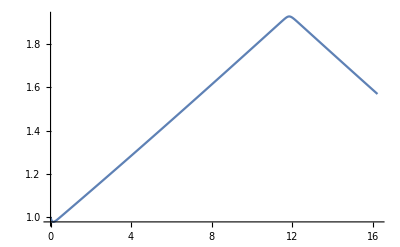

```mathematica
Plot[sol[1,1,1,1,1,1][t],{t,0,Max[time1]}]
```

## Cauchy Stress

```mathematica
T1=mu0 Be
```

{{mu0/Fe3[t],0,0},{0,mu0/Fe3[t],0},{0,0,mu0 Fe3[t]^2}}

```mathematica
T2I=rhohat D[W2,I4] TensorProduct[Fe.n1,Fe.n1]/.{I4->Ce.n1.n1}/.{θ̂->θ,ϕ̂->ϕ}
```

{{(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ]^2 g33[t] Sin[θ]^2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] l[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ] g33[t] Sin[θ]^2 Sin[ϕ] (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] l[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ]^2 √l[t] Sin[θ] (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] √g33[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))},{(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ] g33[t] Sin[θ]^2 Sin[ϕ] (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] l[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) g33[t] Sin[θ]^2 Sin[ϕ]^2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] l[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ] √l[t] Sin[θ] Sin[ϕ] (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] √g33[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))},{(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ]^2 √l[t] Sin[θ] (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] √g33[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ] √l[t] Sin[θ] Sin[ϕ] (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] √g33[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ]^2 l[t]^2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] g33[t]^2 (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))}}

{{(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ]^2 g33[t] Sin[θ]^2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] l[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ] g33[t] Sin[θ]^2 Sin[ϕ] (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] l[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ]^2 √l[t] Sin[θ] (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] √g33[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))},{(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ] g33[t] Sin[θ]^2 Sin[ϕ] (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] l[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) g33[t] Sin[θ]^2 Sin[ϕ]^2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] l[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ] √l[t] Sin[θ] Sin[ϕ] (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] √g33[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))},{(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ]^2 √l[t] Sin[θ] (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] √g33[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ] √l[t] Sin[θ] Sin[ϕ] (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] √g33[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),(2 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+mu2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t])^2) g33^3 mu1 √(2/π) Cos[ϕ]^2 l[t]^2 (-1+(Cos[ϕ]^2 l[t]^2)/g33[t]^2+(Cos[ϕ]^2 g33[t] Sin[θ]^2)/l[t]+(g33[t] Sin[θ]^2 Sin[ϕ]^2)/l[t]))/(Erfi[√2 √b] g33[t]^2 (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))}}

```mathematica
Fe
```

{{(√g33[t])/(√l[t]),0,0},{0,(√g33[t])/(√l[t]),0},{0,0,l[t]/g33[t]}}

```mathematica
D[W2,I4]
```

ⅇ^((-1+I4)^2 mu2) (-1+I4) mu1

```mathematica
n1
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[ϕ]}

```mathematica
(√b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) g33^3 Sin[θ]^3)/(√(2 π) Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))/.{θ->"th"}
```

(√b ⅇ^((2 b Cos[th]^2)/(Cos[th]^2+g33^3 Sin[th]^2)) g33^3 Sin[th]^3)/(√(2 π) Erfi[√2 √b] (Cos[th]^2+g33^3 Sin[th]^2)^(3/2))

```mathematica
PrintMatlab[%]
```

b.^(1/2).*exp(1).^(2.*b.*cos(th).^2.*(cos(th).^2+g33.^3.* ...
  sin(th).^2).^(-1)).*g33.^3.*(2.*pi).^(-1/2).*Erfi(2.^(1/2).* ...
  b.^(1/2)).^(-1).*sin(th).^3.*(cos(th).^2+g33.^3.*sin(th).^2) ...
  .^(-3/2);

```mathematica
-((√b ⅇ^((mu2 (g33^3-2 g33^2 λ+λ^3-g33^3 Cos[2 θ]+λ^3 Cos[2 ϕ])^2)/(4 g33^4 λ^2)+(2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) mu1 (-g33^3+2 g33^2 λ-λ^3+g33^3 Cos[2 θ]-λ^3 Cos[2 ϕ]) (-g33^3+2 λ^3+g33^3 Cos[2 θ]+2 λ^3 Cos[2 ϕ]) )/(2 g33^2 √(2 π) λ^2 Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))) Sin[θ]/.{θ->"th",ϕ->"ph",λ->"l",b->"binitial"}
```

-((√binitial ⅇ^((mu2 (l^3-2 l g33^2+g33^3+l^3 Cos[2 ph]-g33^3 Cos[2 th])^2)/(4 l^2 g33^4)+(2 binitial Cos[th]^2)/(Cos[th]^2+g33^3 Sin[th]^2)) mu1 (-l^3+2 l g33^2-g33^3-l^3 Cos[2 ph]+g33^3 Cos[2 th]) (2 l^3-g33^3+2 l^3 Cos[2 ph]+g33^3 Cos[2 th]) Sin[th])/(2 l^2 g33^2 √(2 π) Erfi[√2 √binitial] (Cos[th]^2+g33^3 Sin[th]^2)^(3/2)))

```mathematica
PrintMatlab[%]
```

(-1/2).*binitial.^(1/2).*l.^(-2).*exp(1).^((1/4).*l.^(-2).* ...
  g33.^(-4).*mu2.*(l.^3+(-2).*l.*g33.^2+g33.^3+l.^3.*cos(2.* ...
  ph)+(-1).*g33.^3.*cos(2.*th)).^2+2.*binitial.*cos(th).^2.*( ...
  cos(th).^2+g33.^3.*sin(th).^2).^(-1)).*g33.^(-2).*mu1.*(2.* ...
  pi).^(-1/2).*((-1).*l.^3+2.*l.*g33.^2+(-1).*g33.^3+(-1).* ...
  l.^3.*cos(2.*ph)+g33.^3.*cos(2.*th)).*(2.*l.^3+(-1).*g33.^3+ ...
  2.*l.^3.*cos(2.*ph)+g33.^3.*cos(2.*th)).*Erfi(2.^(1/2).* ...
  binitial.^(1/2)).^(-1).*sin(th).*(cos(th).^2+g33.^3.*sin(th) ...
  .^2).^(-3/2);

```mathematica
-((√b ⅇ^((mu2 (g33^3-2 g33^2 λ+λ^3-g33^3 Cos[2 θ]+λ^3 Cos[2 ϕ])^2)/(4 g33^4 λ^2)+(2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) mu1 (-g33^3+2 g33^2 λ-λ^3+g33^3 Cos[2 θ]-λ^3 Cos[2 ϕ]) (-g33^3+2 λ^3+g33^3 Cos[2 θ]+2 λ^3 Cos[2 ϕ]) )/(2 g33^2 √(2 π) λ^2 Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))) Sin[θ]/.{θ->"th",ϕ->"ph",λ->"l",b->"binitial"}
```

-((√binitial ⅇ^((mu2 (l^3-2 l g33^2+g33^3+l^3 Cos[2 ph]-g33^3 Cos[2 th])^2)/(4 l^2 g33^4)+(2 binitial Cos[th]^2)/(Cos[th]^2+g33^3 Sin[th]^2)) mu1 (-l^3+2 l g33^2-g33^3-l^3 Cos[2 ph]+g33^3 Cos[2 th]) (2 l^3-g33^3+2 l^3 Cos[2 ph]+g33^3 Cos[2 th]) Sin[th])/(2 l^2 g33^2 √(2 π) Erfi[√2 √binitial] (Cos[th]^2+g33^3 Sin[th]^2)^(3/2)))

```mathematica
PrintMatlab[%]
```

(-1/2).*binitial.^(1/2).*l.^(-2).*exp(1).^((1/4).*l.^(-2).* ...
  g33.^(-4).*mu2.*(l.^3+(-2).*l.*g33.^2+g33.^3+l.^3.*cos(2.* ...
  ph)+(-1).*g33.^3.*cos(2.*th)).^2+2.*binitial.*cos(th).^2.*( ...
  cos(th).^2+g33.^3.*sin(th).^2).^(-1)).*g33.^(-2).*mu1.*(2.* ...
  pi).^(-1/2).*((-1).*l.^3+2.*l.*g33.^2+(-1).*g33.^3+(-1).* ...
  l.^3.*cos(2.*ph)+g33.^3.*cos(2.*th)).*(2.*l.^3+(-1).*g33.^3+ ...
  2.*l.^3.*cos(2.*ph)+g33.^3.*cos(2.*th)).*Erfi(2.^(1/2).* ...
  binitial.^(1/2)).^(-1).*sin(th).*(cos(th).^2+g33.^3.*sin(th) ...
  .^2).^(-3/2);

```mathematica
((3 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) (-1+ⅇ^((mu2 (g33^3-2 g33^2 λ+λ^3-g33^3 Cos[2 θ]+λ^3 Cos[2 ϕ])^2)/(4 g33^4 λ^2))) g33^2 mu1 (8 Cos[θ]^4-4 g33^6 Sin[θ]^4+(1-4 b) g33^3 Sin[2 θ]^2) )/(4 mu2 √(2 π) Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(7/2))) Sin[θ]/.{θ->"th",ϕ->"ph",λ->l}
```

(3 √b ⅇ^((2 b Cos[th]^2)/(Cos[th]^2+g33^3 Sin[th]^2)) (-1+ⅇ^((mu2 (g33^3-2 g33^2 l+l^3+l^3 Cos[2 ph]-g33^3 Cos[2 th])^2)/(4 g33^4 l^2))) g33^2 mu1 Sin[th] (8 Cos[th]^4-4 g33^6 Sin[th]^4+(1-4 b) g33^3 Sin[2 th]^2))/(4 mu2 √(2 π) Erfi[√2 √b] (Cos[th]^2+g33^3 Sin[th]^2)^(7/2))

```mathematica
PrintMatlab[%]
```

(3/4).*b.^(1/2).*exp(1).^(2.*b.*cos(th).^2.*(cos(th).^2+ ...
  g33.^3.*sin(th).^2).^(-1)).*((-1)+exp(1).^((1/4).*g33.^(-4) ...
  .*l.^(-2).*mu2.*(g33.^3+(-2).*g33.^2.*l+l.^3+l.^3.*cos(2.* ...
  ph)+(-1).*g33.^3.*cos(2.*th)).^2)).*g33.^2.*mu1.*mu2.^(-1).* ...
  (2.*pi).^(-1/2).*Erfi(2.^(1/2).*b.^(1/2)).^(-1).*sin(th).*( ...
  cos(th).^2+g33.^3.*sin(th).^2).^(-7/2).*(8.*cos(th).^4+(-4) ...
  .*g33.^6.*sin(th).^4+(1+(-4).*b).*g33.^3.*sin(2.*th).^2);

```mathematica
-((√b ⅇ^((mu2 (g33^3-2 g33^2 λ+λ^3-g33^3 Cos[2 θ]+λ^3 Cos[2 ϕ])^2)/(4 g33^4 λ^2)+(2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)) mu1 (-g33^3+2 g33^2 λ-λ^3+g33^3 Cos[2 θ]-λ^3 Cos[2 ϕ]) (-g33^3+2 λ^3+g33^3 Cos[2 θ]+2 λ^3 Cos[2 ϕ]) )/(2 g33^2 √(2 π) λ^2 Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))) Sin[θ]/.{θ->"th",ϕ->"ph",λ->l}
```

-((√b ⅇ^((mu2 (g33^3-2 g33^2 l+l^3+l^3 Cos[2 ph]-g33^3 Cos[2 th])^2)/(4 g33^4 l^2)+(2 b Cos[th]^2)/(Cos[th]^2+g33^3 Sin[th]^2)) mu1 (-g33^3+2 g33^2 l-l^3-l^3 Cos[2 ph]+g33^3 Cos[2 th]) (-g33^3+2 l^3+2 l^3 Cos[2 ph]+g33^3 Cos[2 th]) Sin[th])/(2 g33^2 l^2 √(2 π) Erfi[√2 √b] (Cos[th]^2+g33^3 Sin[th]^2)^(3/2)))

```mathematica
PrintMatlab[%]
```

(-1/2).*b.^(1/2).*exp(1).^((1/4).*g33.^(-4).*l.^(-2).*mu2.*( ...
  g33.^3+(-2).*g33.^2.*l+l.^3+l.^3.*cos(2.*ph)+(-1).*g33.^3.* ...
  cos(2.*th)).^2+2.*b.*cos(th).^2.*(cos(th).^2+g33.^3.*sin(th) ...
  .^2).^(-1)).*g33.^(-2).*l.^(-2).*mu1.*(2.*pi).^(-1/2).*((-1) ...
  .*g33.^3+2.*g33.^2.*l+(-1).*l.^3+(-1).*l.^3.*cos(2.*ph)+ ...
  g33.^3.*cos(2.*th)).*((-1).*g33.^3+2.*l.^3+2.*l.^3.*cos(2.* ...
  ph)+g33.^3.*cos(2.*th)).*Erfi(2.^(1/2).*b.^(1/2)).^(-1).* ...
  sin(th).*(cos(th).^2+g33.^3.*sin(th).^2).^(-3/2);

```mathematica
1.0e+03*[7.096703326385353, 0.001019006616057, 0.002012747764451, 0.001000000000000, 0.001000000000000]
```

```mathematica
ftermbar1[7.096703326385353 10^3, 0.001019006616057 10^3,0.002012747764451 10^3,1,1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-1.37536329729378×10^21058071

```mathematica
((2 rhohat D[W2,I4] TensorProduct[n1,n1]/.{θ̂->θ}/.{I4->Ce.n1.n1})[[3,3]]-(2 rhohat D[W2,I4] TensorProduct[n1,n1]/.{θ̂->θ}/.{I4->Ce.n1.n1})[[1,1]]) Sin[θ]//Simplify
```

(4 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+(mu2 (-g33[t]^2 l[t]+Cos[ϕ]^2 l[t]^3+g33[t]^3 Sin[θ]^2)^2)/(g33[t]^4 l[t]^2)) g33^3 mu1 √(2/π) Cos[θ]^2 Cos[ϕ]^2 Sin[θ] (-g33[t]^2 l[t]+Cos[ϕ]^2 l[t]^3+g33[t]^3 Sin[θ]^2))/(Erfi[√2 √b] g33[t]^2 l[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))

```mathematica
(4 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+(mu2 (-g33[t]^2 l[t]+Cos[ϕ]^2 l[t]^3+g33[t]^3 Sin[θ]^2)^2)/(g33[t]^4 l[t]^2)) g33^3 mu1 √(2/π) Cos[θ]^2 Cos[ϕ]^2 Sin[θ] (-g33[t]^2 l[t]+Cos[ϕ]^2 l[t]^3+g33[t]^3 Sin[θ]^2))/(Erfi[√2 √b] g33[t]^2 l[t] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))/.{g33[t]->g33,l[t]->λ}
```

(4 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+(mu2 (-g33^2 λ+λ^3 Cos[ϕ]^2+g33^3 Sin[θ]^2)^2)/(g33^4 λ^2)) g33 mu1 √(2/π) Cos[θ]^2 Cos[ϕ]^2 Sin[θ] (-g33^2 λ+λ^3 Cos[ϕ]^2+g33^3 Sin[θ]^2))/(λ Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2))

```mathematica
TAng[g33_?NumericQ,λ_?NumericQ,b_?NumericQ,mu1_?NumericQ,mu2_?NumericQ]:=NIntegrate[(4 √b ⅇ^((2 b Cos[θ]^2)/(Cos[θ]^2+g33^3 Sin[θ]^2)+(mu2 (-g33^2 λ+λ^3 Cos[ϕ]^2+g33^3 Sin[θ]^2)^2)/(g33^4 λ^2)) g33 mu1 √(2/π) Cos[θ]^2 Cos[ϕ]^2 Sin[θ] (-g33^2 λ+λ^3 Cos[ϕ]^2+g33^3 Sin[θ]^2))/(λ Erfi[√2 √b] (Cos[θ]^2+g33^3 Sin[θ]^2)^(3/2)),{θ,0,π},{ϕ,0,2 π}]
```

```mathematica
TIso=-(mu0 g33[t])/l[t]+(mu0 l[t]^2)/g33[t]^2
```

-(mu0 g33[t])/l[t]+(mu0 l[t]^2)/g33[t]^2

```mathematica
Ttot=TIso+TAng[g33[t],l[t],b,mu1,mu2]
```

-(mu0 g33[t])/l[t]+(mu0 l[t]^2)/g33[t]^2+TAng[g33[t],l[t],b,mu1,mu2]